```mathematica
$MaxExtraPrecision=1000;
mpprec=100;
(*wα=0;*)
wα=-1/2;
norm[k_,α_,β_]:=If[k==0,√(1/2(Gamma[α+1]Gamma[β+1])/Gamma[α+β+2]),√(1/(2(2k+α+β+1))(Gamma[k+α+1]Gamma[k+β+1])/(Gamma[k+α+β+1]Gamma[k+1]))];
wgrid[n_]:=N[Table[Cos[(2k-1)/(4n)π],{k,n,1,-1}],mpprec]
wweights[n_]:=Table[π/(2n),{k,1,n}]
Wnl[n_,l_,r_]:=r^l JacobiP[n,wα,l-1/2,2 r^2-1]/norm[n,wα,l-1/2]
```

```mathematica
rd[f_,l_,t_]:=Module[{out},
out = Simplify[t D[f,t]];
out]
dr[f_,l_,t_]:=Module[{out},
out = Simplify[D[r f,t]];
out]
divrd[f_,l_,t_]:=Module[{out},
out = Simplify[1/t D[f,t]];
out]
divrdr[f_,l_,t_]:=Module[{out},
out = Simplify[1/t D[t f,t]];
out]
divr[f_,m_,t_]:=Module[{out,bad},
out = Simplify[1/t f];
out]
divr2[f_,m_,t_]:=Module[{out,bad},
out = Simplify[1/t^2 f];
out]
divrClean[f_,m_,t_]:=Module[{out,bad},
out = Simplify[1/t f];
bad=Coefficient[out,t,m];
out-=bad t^m;
out]
divr2Clean[f_,m_,t_]:=Module[{out,bad},
out = Simplify[1/t^2 f];
bad=Coefficient[out,t,m];
out-=bad t^m;
out]
divrdClean[f_,m_,t_]:=Module[{out,bad},
out = Simplify[1/t D[f,t]];
bad=Coefficient[out,t,m];
out-=bad t^m;
out]
divrdrClean[f_,m_,t_]:=Module[{out,bad},
out = Simplify[1/t D[t f,t]];
bad=Coefficient[out,t,m];
out-=bad t^m;
out]
```

```mathematica
i1Mat[spec_,l_]:=Module[{grid,wgts,s,gN,nN,p}, 
nN=Length[spec];
gN=Max[nN+Floor[l/2]+5,10];
grid=wgrid[gN];
wgts=wweights[gN];
s=Total[ParallelTable[ r^l Integrate[4 r^(1-l)Wnl[i-1,l, r] spec[[i]],r],{i,1,nN}]];
p=s/.{r->grid};
If[!VectorQ[p],p=0 grid;];
s=ParallelTable[Dot[wgts Wnl[i-1,l,grid], p],{i,1,nN}];
s];
i2Mat[row_,nN_,l_,gfunc_, wfunc_]:=Module[{bad,grid,wgts,s,gN,p}, 
gN=Max[nN+Floor[l/2]+10,10];
grid=gfunc[gN];
wgts=wfunc[gN];
s= Wnl[row,l, r];
s=  r^l Integrate[4r Integrate[4 r^(1-l)s,r],r];
p=s/.{r->grid};
If[!VectorQ[p],p=0 grid];
s=ParallelTable[Dot[wgts Wnl[i,l,grid], p],{i,0,nN-1}];
s];
r2Mat[row_,nN_,l_,gfunc_, wfunc_]:=Module[{grid,wgts,s,gN,p}, 
gN=Max[nN+Floor[l/2]+10,10];
grid=gfunc[gN];
wgts=wfunc[gN];
s= r^2 Wnl[row,l, r];
p=s/.{r->grid};
If[!VectorQ[p],p=0 grid;];
s=ParallelTable[Dot[wgts Wnl[i,l,grid], p],{i,0,nN-1}];
s];
rdMat[row_,nN_,l_,gfunc_, wfunc_]:=Module[{grid,wgts,s,gN,p}, 
gN=Max[nN+Floor[l/2]+10,10];
grid=gfunc[gN];
wgts=wfunc[gN];
s=rd[Wnl[row,1,r],l-2,r];
p=s/.{r->grid};
If[!VectorQ[p],p=0 grid;];
s=ParallelTable[Dot[wgts Wnl[i,l,grid], p],{i,0,nN-1}];
s];
divrdrMat[row_,nN_,l_,gfunc_, wfunc_]:=Module[{grid,wgts,s,gN,p}, 
gN=Max[nN+Floor[l/2]+10,10];
grid=gfunc[gN];
wgts=wfunc[gN];
s=divrdrClean[ Wnl[row,l-1, r],l-2,r];
p=s/.{r->grid};
If[!VectorQ[p],p=0 grid;];
s=ParallelTable[Dot[wgts Wnl[i,l,grid], p],{i,0,nN-1}];
s];
divrMat[row_,nN_,l_,gfunc_, wfunc_]:=Module[{grid,wgts,s,gN,p}, 
gN=Max[nN+Floor[l/2]+10,10];
grid=gfunc[gN];
wgts=wfunc[gN];
s=divrClean[Wnl[row,l-1, r],l-2,r];
p=s/.{r->grid};
If[!VectorQ[p],p=0 grid];
s=ParallelTable[Dot[wgts Wnl[i,l,grid], p],{i,0,nN-1}];
s];
divr2Mat[row_,nN_,l_,gfunc_, wfunc_]:=Module[{grid,wgts,s,gN,p}, 
gN=Max[nN+Floor[l/2]+10,10];
grid=gfunc[gN];
wgts=wfunc[gN];
s=divr2Clean[Wnl[row,l, r],l-2,r];
p=s/.{r->grid};
If[!VectorQ[p],p=0 grid];
s=ParallelTable[Dot[wgts Wnl[i,l,grid], p],{i,0,nN-1}];
s];
divr2Matb[row_,nN_,l_,gfunc_, wfunc_]:=Module[{grid,wgts,s,gN,p}, 
gN=Max[nN+Floor[l/2]+10,10];
grid=gfunc[gN];
wgts=wfunc[gN];
s=divr2Clean[Wnl[row,l, r],l-2,r];
p=s/.{r->grid};
If[!VectorQ[p],p=0 grid];
s=ParallelTable[Dot[wgts Wnl[i,l-2,grid], p],{i,0,nN-1}];
s];
divrdMat[row_,nN_,l_,gfunc_, wfunc_]:=Module[{grid,wgts,s,gN,p}, 
gN=Max[nN+Floor[l/2]+10,10];
grid=gfunc[gN];
wgts=wfunc[gN];
s=divrdClean[Wnl[row,l, r],l-2,r];
p=s/.{r->grid};
If[!VectorQ[p],p=0 grid];
s=ParallelTable[Dot[wgts Wnl[i,l,grid], p],{i,0,nN-1}];
s];
divrdMatb[row_,nN_,l_,gfunc_, wfunc_]:=Module[{grid,wgts,s,gN,p}, 
gN=Max[nN+Floor[l/2]+10,10];
grid=gfunc[gN];
wgts=wfunc[gN];
s=divrdClean[Wnl[row,l, r],l-2,r];
p=s/.{r->grid};
If[!VectorQ[p],p=0 grid];
s=ParallelTable[Dot[wgts Wnl[i,l-2,grid], p],{i,0,nN-1}];
s];
i2divrdMat[row_,nN_,l_,gfunc_, wfunc_]:=Module[{bad,grid,wgts,s,gN,p}, 
gN=Max[nN+Floor[l/2]+10,10];
grid=gfunc[gN];
wgts=wfunc[gN];
s=divrdClean[Wnl[row,l, r],l-2,r];
s=  r^l Integrate[4r Integrate[4 r^(1-l)s,r],r];
p=s/.{r->grid};
If[!VectorQ[p],p=0 grid];
s=ParallelTable[Dot[wgts Wnl[i,l,grid], p],{i,0,nN-1}];
s];
i2divr2Mat[row_,nN_,l_,gfunc_, wfunc_]:=Module[{bad,grid,wgts,s,gN,p}, 
gN=Max[nN+Floor[l/2]+10,10];
grid=gfunc[gN];
wgts=wfunc[gN];
s=divr2Clean[Wnl[row,l, r],l-2,r];
s=  r^l Integrate[4r Integrate[4 r^(1-l)s,r],r];
p=s/.{r->grid};
If[!VectorQ[p],p=0 grid];
s=ParallelTable[Dot[wgts Wnl[i,l,grid], p],{i,0,nN-1}];
s];
```

```mathematica
divrDirty[row_,nN_,l_,gfunc_, wfunc_]:=Module[{grid,wgts,s,gN,p}, 
gN=Max[nN+Floor[l/2]+10,10];
grid=gfunc[gN];
wgts=wfunc[gN];
s=divr[Wnl[row,l-1, r],l-2,r];
p=s/.{r->grid};
If[!VectorQ[p],p=0 grid];
s=ParallelTable[Dot[wgts Wnl[i,l,grid], p],{i,0,nN-1}];
s];
divr2Dirty[row_,nN_,l_,gfunc_, wfunc_]:=Module[{grid,wgts,s,gN,p}, 
gN=Max[nN+Floor[l/2]+10,10];
grid=gfunc[gN];
wgts=wfunc[gN];
s=divr2[Wnl[row,l, r],l-2,r];
p=s/.{r->grid};
If[!VectorQ[p],p=0 grid];
s=ParallelTable[Dot[wgts Wnl[i,l,grid], p],{i,0,nN-1}];
s];
divr2Dirtyb[row_,nN_,l_,gfunc_, wfunc_]:=Module[{grid,wgts,s,gN,p}, 
gN=Max[nN+Floor[l/2]+10,10];
grid=gfunc[gN];
wgts=wfunc[gN];
s=divr2[Wnl[row,l, r],l-2,r];
p=s/.{r->grid};
If[!VectorQ[p],p=0 grid];
s=ParallelTable[Dot[wgts Wnl[i,l-2,grid], p],{i,0,nN-1}];
s];
divrdDirty[row_,nN_,l_,gfunc_, wfunc_]:=Module[{grid,wgts,s,gN,p}, 
gN=Max[nN+Floor[l/2]+10,10];
grid=gfunc[gN];
wgts=wfunc[gN];
s=divrd[Wnl[row,l, r],l-2,r];
p=s/.{r->grid};
If[!VectorQ[p],p=0 grid];
s=ParallelTable[Dot[wgts Wnl[i,l,grid], p],{i,0,nN-1}];
s];
divrdDirtyb[row_,nN_,l_,gfunc_, wfunc_]:=Module[{grid,wgts,s,gN,p}, 
gN=Max[nN+Floor[l/2]+10,10];
grid=gfunc[gN];
wgts=wfunc[gN];
s=divrd[Wnl[row,l, r],l-2,r];
p=s/.{r->grid};
If[!VectorQ[p],p=0 grid];
s=ParallelTable[Dot[wgts Wnl[i,l-2,grid], p],{i,0,nN-1}];
s];
i2divrdDirty[row_,nN_,l_,gfunc_, wfunc_]:=Module[{grid,wgts,s,gN,p}, 
gN=Max[nN+Floor[l/2]+10,10];
grid=gfunc[gN];
wgts=wfunc[gN];
s=divrd[Wnl[row,l, r],l-2,r];
s=  r^l Integrate[4r Integrate[4 r^(1-l)s,r],r];
p=s/.{r->grid};
If[!VectorQ[p],p=0 grid];
s=ParallelTable[Dot[wgts Wnl[i,l,grid], p],{i,0,nN-1}];
s];
```

```mathematica
upLMat[row_,nN_,l_,gfunc_, wfunc_]:=Module[{grid,wgts,s,gN,p}, 
gN=Max[nN+Floor[l/2]+10,10];
grid=gfunc[gN];
wgts=wfunc[gN];
s=Wnl[row,l-2, r];
p=s/.{r->grid};
If[!VectorQ[p],p=0 grid];
s=ParallelTable[Dot[wgts Wnl[i,l,grid], p],{i,0,nN-1}];
s];
```

```mathematica
nN=8;
l=18;
iN = 3;
gN =Floor[ 3/2(nN+l/2+10)];
f=Sum[Wnl[i,l,r],{i,0,iN-1}];
grid = wgrid[gN];
weights=wweights[gN];
```

```mathematica
vIn =Table[0,{i,0,nN-1}];
fg =f/.{r->grid};
If[!VectorQ[fg],fg=0 grid;];
vIn[[1;;iN]]=ParallelTable[Dot[weights Wnl[i, l, grid], fg],{i,0,iN-1}];
vIn//N
```

{1.,1.,1.,0.,0.,0.,0.,0.}

```mathematica
vOut =Table[0,{i,0,nN-1}];
tf=divrdClean[f,l-2,r];
tf//Expand//N
fg =tf/.{r->grid};
If[!VectorQ[fg],fg=0 grid;];
vOut[[1;;iN]] = ParallelTable[Dot[weights Wnl[i, l, grid], fg],{i,0,iN-1}];
vOut//N
Clear[tf];
```

-28876.7 r^18+17830.6 r^20

{-5244.75,290.679,0.,0.,0.,0.,0.,0.}

```mathematica
mDivR2=Transpose[Table[divr2Mat[i,nN,l,wgrid,wweights],{i,0,nN-1}]];
mDivR2b=Transpose[Table[divr2Matb[i,nN,l,wgrid,wweights],{i,0,nN-1}]];

mDivR2//N//MatrixForm
mDivR2b//N//MatrixForm
mUpL//N//MatrixForm
```

(0. | 27.9382 | -326.118 | 2518.46 | -14886.1 | 72457.8 | -303534. | 1.12695×10^6
0. | 0. | 13.2127 | -102.852 | 608.025 | -2959.56 | 12397.9 | -46030.6
0. | 0. | 0. | 9.53064 | -57.3508 | 279.305 | -1170.07 | 4344.2
0. | 0. | 0. | 0. | 7.85488 | -39.4013 | 165.275 | -613.677
0. | 0. | 0. | 0. | 0. | 6.90296 | -30.2103 | 112.452
0. | 0. | 0. | 0. | 0. | 0. | 6.29336 | -24.7676
0. | 0. | 0. | 0. | 0. | 0. | 0. | 5.87223
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

(0. | 27.9147 | -326.383 | 2520.58 | -14898.6 | 72518.8 | -303790. | 1.1279×10^6
0. | 1.14535 | -0.227567 | 0.0506316 | -0.0129622 | 0.0037478 | -0.00120028 | 0.000419072
0. | 0. | 1.25409 | -0.37119 | 0.106686 | -0.0328406 | 0.0109368 | -0.00392136
0. | 0. | 0. | 1.356 | -0.518667 | 0.179304 | -0.063592 | 0.0237156
0. | 0. | 0. | 0. | 1.45148 | -0.667968 | 0.26612 | -0.105716
0. | 0. | 0. | 0. | 0. | 1.54098 | -0.817453 | 0.364859
0. | 0. | 0. | 0. | 0. | 0. | 1.62494 | -0.965877
0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.70377)

(0.999802 | 0.0199093 | -0.000458463 | 0.0000316348 | -3.54335×10^-6 | 5.37061×10^-7 | -1.00905×10^-7 | 2.23268×10^-8
-0.0198667 | 0.998733 | 0.0462113 | -0.0016005 | 0.000143907 | -0.0000195351 | 3.43529×10^-6 | -7.2744×10^-7
0.00137015 | -0.0459698 | 0.996519 | 0.0694657 | -0.00313546 | 0.000341612 | -0.0000537886 | 0.0000106576
-0.000157361 | 0.00475685 | -0.068749 | 0.993497 | 0.0904923 | -0.00495145 | 0.000625721 | -0.000110993
0.0000246492 | -0.000710363 | 0.00924593 | -0.0889713 | 0.989911 | 0.109662 | -0.00696414 | 0.000991561
-4.79917×10^-6 | 0.000134593 | -0.00166963 | 0.0144625 | -0.107001 | 0.985933 | 0.127241 | -0.00911133
1.10123×10^-6 | -0.000030349 | 0.000366288 | -0.00302314 | 0.0201246 | -0.123122 | 0.981692 | 0.14344
-2.87786×10^-7 | 7.8358×10^-6 | -0.000092917 | 0.000745979 | -0.00473037 | 0.0260271 | -0.137573 | 0.977282)

```mathematica
mUpL=Transpose[Table[upLMat[i,nN,l,wgrid,wweights],{i,0,nN-1}]];
mUpL//N//MatrixForm
```

(0.999159 | 0.040996 | 0. | 0. | 0. | 0. | 0. | 0.
-0.0408109 | 0.994648 | 0.0949158 | 0. | 0. | 0. | 0. | 0.
0.00385158 | -0.0938712 | 0.985358 | 0.142278 | 0. | 0. | 0. | 0.
-0.000544092 | 0.0132607 | -0.139196 | 0.972781 | 0.184787 | 0. | 0. | 0.
0.0000997214 | -0.00243042 | 0.0255119 | -0.178292 | 0.957978 | 0.223235 | 0. | 0.
-0.0000220632 | 0.000537728 | -0.00564448 | 0.0394468 | -0.211951 | 0.941712 | 0.258199 | 0.
5.643×10^-6 | -0.000137532 | 0.00144366 | -0.0100891 | 0.0542097 | -0.240857 | 0.924535 | 0.29014
-1.62122×10^-6 | 0.0000395125 | -0.00041476 | 0.00289857 | -0.0155743 | 0.0691975 | -0.265616 | 0.906845)

```mathematica
dDivR2b=Transpose[Table[divr2Dirtyb[i,nN,l,wgrid,wweights],{i,0,nN-1}]];
dDivR2b//N//MatrixForm
```

(1.02944 | -0.089042 | 0.0133055 | -0.00263802 | 0.000634591 | -0.000176506 | 0.000055062 | -0.0000188651
0. | 1.14535 | -0.227567 | 0.0506316 | -0.0129622 | 0.0037478 | -0.00120028 | 0.000419072
0. | 0. | 1.25409 | -0.37119 | 0.106686 | -0.0328406 | 0.0109368 | -0.00392136
0. | 0. | 0. | 1.356 | -0.518667 | 0.179304 | -0.063592 | 0.0237156
0. | 0. | 0. | 0. | 1.45148 | -0.667968 | 0.26612 | -0.105716
0. | 0. | 0. | 0. | 0. | 1.54098 | -0.817453 | 0.364859
0. | 0. | 0. | 0. | 0. | 0. | 1.62494 | -0.965877
0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.70377)

```mathematica
mDivRD=Transpose[Table[divrdMat[i,nN,l,wgrid,wweights],{i,0,nN-1}]];
mDivRDb=Transpose[Table[divrdMatb[i,nN,l,wgrid,wweights],{i,0,nN-1}]];
mDivRD//N//MatrixForm
mDivRDb//N//MatrixForm
mDivRD.vIn//N
mDivRDb.vIn//N
```

(0. | 558.763 | -5803.51 | 45409.7 | -267863. | 1.30434×10^6 | -5.46351×10^6 | 2.02852×10^7
0. | 0. | 290.679 | -1795.02 | 11008.5 | -53201.3 | 223240. | -828467.
0. | 0. | 0. | 228.735 | -976.071 | 5091.22 | -20991.9 | 78270.7
0. | 0. | 0. | 0. | 204.227 | -651.386 | 3040.78 | -10975.6
0. | 0. | 0. | 0. | 0. | 193.283 | -483.864 | 2093.05
0. | 0. | 0. | 0. | 0. | 0. | 188.801 | -383.661
0. | 0. | 0. | 0. | 0. | 0. | 0. | 187.911
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

(0. | 558.293 | -5810.5 | 45445.6 | -268091. | 1.30543×10^6 | -5.46811×10^6 | 2.03023×10^7
0. | 22.9071 | 51.2025 | 54.7272 | 62.6465 | 69.0345 | 75.5205 | 81.7547
0. | 0. | 27.59 | 55.0103 | 54.6782 | 62.6365 | 67.7732 | 73.6207
0. | 0. | 0. | 32.5439 | 59.7949 | 56.2501 | 65.0496 | 69.1346
0. | 0. | 0. | 0. | 37.7385 | 64.7929 | 58.3512 | 68.4503
0. | 0. | 0. | 0. | 0. | 43.1475 | 69.7808 | 60.684
0. | 0. | 0. | 0. | 0. | 0. | 48.7482 | 74.6697
0. | 0. | 0. | 0. | 0. | 0. | 0. | 54.5206)

{-5244.75,290.679,0.,0.,0.,0.,0.,0.}

{-5252.2,74.1095,27.59,0.,0.,0.,0.,0.}

```mathematica
dDivRD=Transpose[Table[divrdDirty[i,nN,l,wgrid,wweights],{i,0,nN-1}]];
dDivRDb=Transpose[Table[divrdDirtyb[i,nN,l,wgrid,wweights],{i,0,nN-1}]];
dDivRD//N//MatrixForm
dDivRDb//N//MatrixForm
dDivRD.vIn//N
dDivRDb.vIn//N
```

(18.5143 | 55.1201 | 66.6827 | 77.3308 | 87.0516 | 96.3027 | 105.24 | 113.964
-0.756221 | 20.5714 | 50.9093 | 56.5887 | 64.0504 | 70.7923 | 77.377 | 83.787
0.0713693 | -1.94145 | 22.6286 | 53.9872 | 56.8301 | 63.6025 | 69.3405 | 75.131
-0.0100819 | 0.274259 | -3.19661 | 24.6857 | 58.3146 | 58.8377 | 65.5736 | 70.6777
0.00184782 | -0.0502663 | 0.585877 | -4.52441 | 26.7429 | 63.1128 | 61.4345 | 68.4851
-0.000408829 | 0.0111213 | -0.129625 | 1.00102 | -5.91683 | 28.8 | 68.1543 | 64.2715
0.000104564 | -0.00284445 | 0.0331534 | -0.256026 | 1.51332 | -7.36603 | 30.8571 | 73.346
-0.000030041 | 0.000817202 | -0.00952488 | 0.0735555 | -0.434771 | 2.11624 | -8.86517 | 32.9143)

(18.5299 | 54.2266 | 64.638 | 75.1504 | 84.5544 | 93.5512 | 102.23 | 110.705
0. | 22.9071 | 51.2025 | 54.7272 | 62.6465 | 69.0345 | 75.5205 | 81.7547
0. | 0. | 27.59 | 55.0103 | 54.6782 | 62.6365 | 67.7732 | 73.6207
0. | 0. | 0. | 32.5439 | 59.7949 | 56.2501 | 65.0496 | 69.1346
0. | 0. | 0. | 0. | 37.7385 | 64.7929 | 58.3512 | 68.4503
0. | 0. | 0. | 0. | 0. | 43.1475 | 69.7808 | 60.684
0. | 0. | 0. | 0. | 0. | 0. | 48.7482 | 74.6697
0. | 0. | 0. | 0. | 0. | 0. | 0. | 54.5206)

{140.317,70.7245,20.7585,-2.93244,0.537458,-0.118912,0.0304135,-0.00873772}

{137.394,74.1095,27.59,0.,0.,0.,0.,0.}

```mathematica
137.39440631681495-5389.598791582751
```

-5252.2

```mathematica
val=Table[Integrate[1/(√(1-r^2))Wnl[0,l-2,r](JacobiP[i,-1/2,l-1/2,-1] 1/r D[r^l,r])/norm[i,-1/2,l-1/2],{r,0,1}],{i,0,iN-1}];
Total[val]//N
```

5389.6

```mathematica
Total[{(1703936 √(66/595))/392863,-(3407872 √(2442/119))/392863,(18743296 √(2886/11305))/20677}]//N
```

420.155

```mathematica
mUpL//N//MatrixForm
```

(0.999159 | 0.040996 | 0. | 0. | 0. | 0. | 0. | 0.
-0.0408109 | 0.994648 | 0.0949158 | 0. | 0. | 0. | 0. | 0.
0.00385158 | -0.0938712 | 0.985358 | 0.142278 | 0. | 0. | 0. | 0.
-0.000544092 | 0.0132607 | -0.139196 | 0.972781 | 0.184787 | 0. | 0. | 0.
0.0000997214 | -0.00243042 | 0.0255119 | -0.178292 | 0.957978 | 0.223235 | 0. | 0.
-0.0000220632 | 0.000537728 | -0.00564448 | 0.0394468 | -0.211951 | 0.941712 | 0.258199 | 0.
5.643×10^-6 | -0.000137532 | 0.00144366 | -0.0100891 | 0.0542097 | -0.240857 | 0.924535 | 0.29014
-1.62122×10^-6 | 0.0000395125 | -0.00041476 | 0.00289857 | -0.0155743 | 0.0691975 | -0.265616 | 0.906845)

```mathematica
mUpL.(dDivRDb.vIn)//N
uUpL = UpperTriangularize[mUpL,1];
uUpL.(dDivRDb.vIn)//N
lUpL = LowerTriangularize[mUpL,-1];
lUpL//N//MatrixForm;
lUpL.(dDivRDb.vIn)//N
dUpL = DiagonalMatrix[Diagonal[mUpL]];
dUpL//N//MatrixForm;
dUpL.(dDivRDb.vIn)//N
```

{140.317,70.7245,20.7585,-2.93244,0.537458,-0.118912,0.0304135,-0.00873772}

{3.03819,2.61873,0.,0.,0.,0.,0.,0.}

{0.,-5.60719,-6.42757,-2.93244,0.537458,-0.118912,0.0304135,-0.00873772}

{137.279,73.7129,27.1861,0.,0.,0.,0.,0.}

```mathematica
q=Wnl[5,l,r];
p= q-Coefficient[q,r,l] r^l;
s=r^l JacobiP[5,-1/2,l-1/2,r^2-1];
t=Wnl[4,l+2,r] norm[4,-1/2,l+1/2]/norm[5,-1/2,l-1/2];
p/.{r->1}//N
s/.{r->1}//N
```

154671.

-157.43

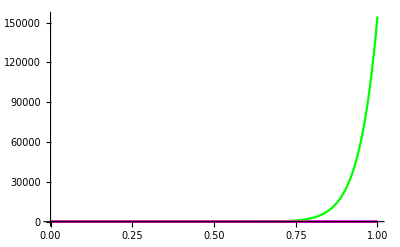

```mathematica
Plot[{q,p,s,t},{r,0,1},PlotStyle->{Blue,Green,Red,Magenta},PlotRange->All]
```

```mathematica
p norm[5,-1/2,l-1/2]/norm[4,-1/2,l+1/2]//Expand//N
Wnl[4,l+2,r]//Expand//N
```

895683. r^20-2.20476×10^6 r^22+2.68873×10^6 r^24-1.62574×10^6 r^26+390179. r^28

47281. r^20-221414. r^22+386187. r^24-297507. r^26+85454.1 r^28